```mathematica
data=Import["../fatal-police-shootings-data.csv"];
```

```mathematica
allDates=data[[2;;, 3]];
years={"2015","2016","2017","2018"};
dates=Select[allDates,StringStartsQ[#,years]&];
```

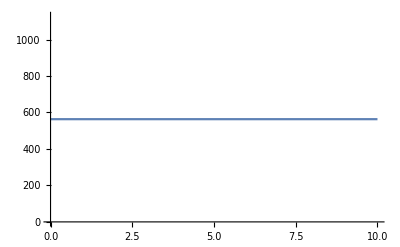

```mathematica
Plot[Length[dates]/7,{x,0,10}]
```

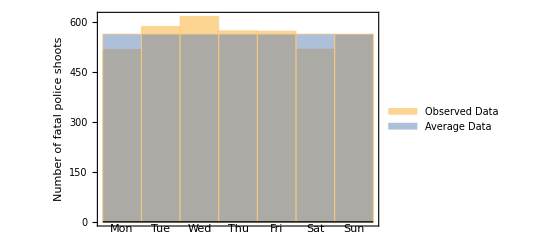

```mathematica
average=WeightedData[DateObject[{0,0,#}]&/@Range[6,12],Table[Length[dates]/7,{i,1,7}]];
fig=DateHistogram[
{Legended[dates,"Observed Data"],
Legended[average,"Average Data"]},
"Day",DateReduction->"Week",
Frame->{True,True,False,False},
FrameLabel->{None,"Number of fatal police shoots"}
]
Export["q4-day.eps",fig];
```

```mathematica
dateObjects=SplitBy[DateObject/@dates,DateList[#][[1]]&];
```

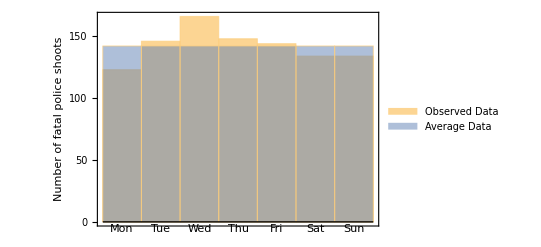
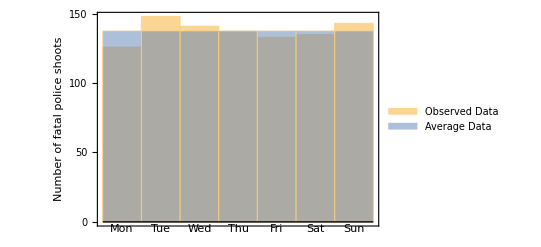
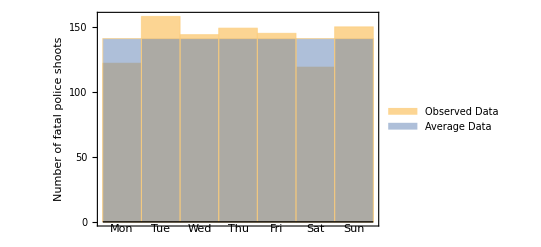
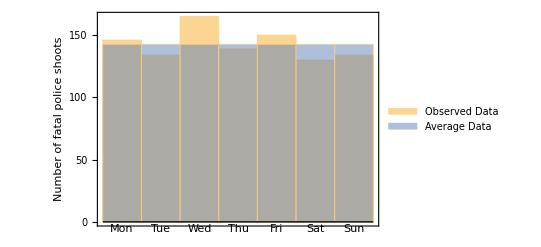

```mathematica
average=Table[WeightedData[DateObject[{0,0,#}]&/@Range[6,12],Table[Length[dateObjects[[j]]]/7,{i,1,7}]],{j,1,4}];
figs=Table[DateHistogram[
{Legended[dateObjects[[i]],"Observed Data"],
Legended[average[[i]],"Average Data"]},
"Day",DateReduction->"Week",
Frame->{True,True,False,False},
FrameLabel->{None,"Number of fatal police shoots"},
FrameTicks->{Automatic,{0,50,100,150}}
],{i,1,Length[years]}]
Export["q4-day-"<>years[[#]]<>".eps",figs[[#]]]&/@Range[1,Length[years]];
```

```mathematica
days=DayName@{0,0,#}&/@Range[6,12];
observe=Table[Lookup[Counts[DayName/@dateObjects[[i]]],days,0],{i,1,Length[years]}];
observe//TableForm
```

123 | 146 | 166 | 148 | 144 | 134 | 134
126 | 148 | 141 | 137 | 133 | 135 | 143
122 | 158 | 144 | 149 | 145 | 119 | 150
146 | 134 | 165 | 139 | 150 | 130 | 134

```mathematica
ni=Table[Sum[observe[[i,j]],{j,1,Length[days]}],{i,1,Length[years]}]
N[ni/Length[days]]
nj=Table[Sum[observe[[i,j]],{i,1,Length[years]}],{j,1,Length[days]}]
n=Sum[ni[[i]],{i,1,Length[years]}]
N[n/Length[days]]
expect=Table[ni[[i]]*nj[[j]]/n,{i,1,Length[years]},{j,1,Length[days]}];
N[expect//TableForm]
```

{995,963,987,998}

{142.143,137.571,141.,142.571}

{517,586,616,573,572,518,561}

3943

563.286

130.463 | 147.875 | 155.445 | 144.594 | 144.342 | 130.715 | 141.566
126.267 | 143.119 | 150.446 | 139.944 | 139.7 | 126.511 | 137.013
129.414 | 146.686 | 154.195 | 143.432 | 143.181 | 129.664 | 140.428
130.856 | 148.321 | 155.914 | 145.03 | 144.777 | 131.109 | 141.993

```mathematica
X2=∑_(i=1)^Length[years] ∑_(j=1)^Length[days] (observe[[i,j]]-expect[[i,j]])^2/expect[[i,j]];
degree=(Length[years]-1)*(Length[days]-1);
N[X2]
1-CDF[ChiSquareDistribution[degree],%]
```

12.0134

0.846545

```mathematica
X2=∑_(j=1)^Length[days] (nj[[j]]-n/Length[days])^2/(n/Length[days]);
degree=Length[days]-1;
N[X2]
1-CDF[ChiSquareDistribution[degree],%]
InverseCDF[ChiSquareDistribution[6],0.95]
```

13.6049

0.0343753

12.5916

```mathematica
X2=Table[∑_(j=1)^Length[days] (observe[[i,j]]-ni[[i]]/Length[days])^2/(ni[[i]]/Length[days]),{i,1,Length[years]}];
degree=Length[days]-1;
N[X2]
```

{189.813,163.725,168.298,131.234}

WeightedData[…]

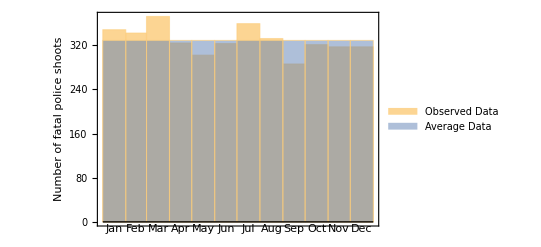

```mathematica
average=WeightedData[DateObject[{0,#,1}]&/@Range[1,12],Table[Length[dates]/12,{i,1,12}]]
fig=DateHistogram[
{Legended[dates,"Observed Data"],
Legended[average,"Average Data"]},
"Month",DateReduction->"Year",
Frame->{True,True,False,False},
FrameLabel->{None,"Number of fatal police shoots"}
]
Export["q4-month.eps",fig];
```

```mathematica
dateObjects=SplitBy[DateObject/@dates,DateList[#][[1]]&];
```

{WeightedData[…],WeightedData[…],WeightedData[…],WeightedData[…]}

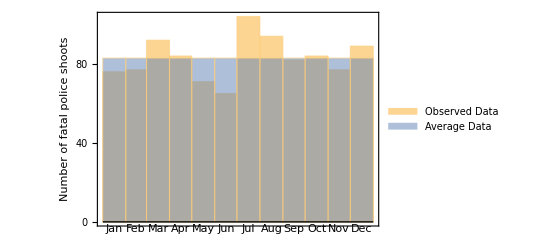
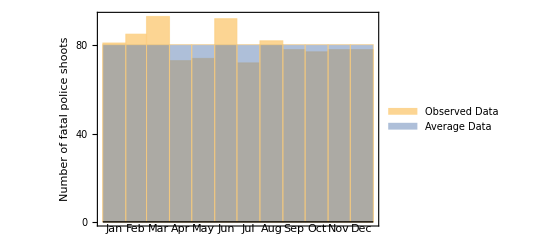
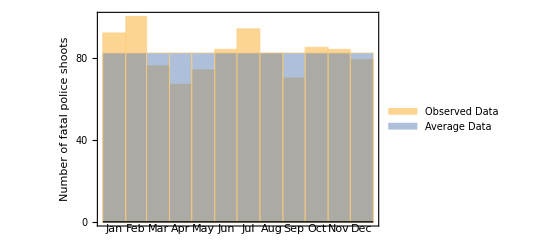
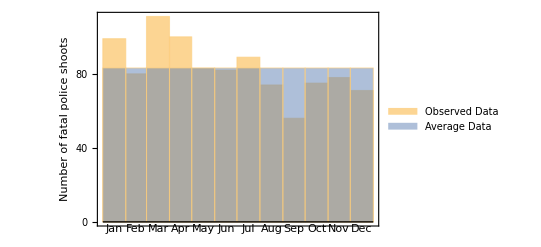

```mathematica
average=Table[WeightedData[DateObject[{0,#,1}]&/@Range[1,12],Table[Length[dateObjects[[j]]]/12,{i,1,12}]],{j,1,4}]
figs=Table[DateHistogram[
{Legended[dateObjects[[i]],"Observed Data"],
Legended[average[[i]],"Average Data"]},
"Month",DateReduction->"Year",
Frame->{True,True,False,False},
FrameLabel->{None,"Number of fatal police shoots"},
FrameTicks->{Automatic,{0,20,40,60,80,100,120}}
],{i,1,Length[years]}]
Export["q4-month-"<>years[[#]]<>".eps",figs[[#]]]&/@Range[1,Length[years]];
```

```mathematica
months=DateString[{0,#,1},"MonthName"]&/@Range[1,12];
observe=Table[Lookup[Counts[DateString[#,"MonthName"]&/@dateObjects[[i]]],months,0],{i,1,Length[years]}];
observe//TableForm
```

76 | 77 | 92 | 84 | 71 | 65 | 104 | 94 | 82 | 84 | 77 | 89
81 | 86 | 92 | 73 | 74 | 92 | 72 | 82 | 78 | 77 | 78 | 78
92 | 100 | 76 | 67 | 74 | 84 | 94 | 82 | 70 | 85 | 84 | 79
99 | 80 | 111 | 100 | 83 | 82 | 89 | 74 | 56 | 75 | 78 | 71

```mathematica
ni=Table[Sum[observe[[i,j]],{j,1,Length[months]}],{i,1,Length[years]}]
N[ni/Length[months]]
nj=Table[Sum[observe[[i,j]],{i,1,Length[years]}],{j,1,Length[months]}]
n=Sum[ni[[i]],{i,1,Length[years]}]
N[n/Length[months]]
expect=Table[ni[[i]]*nj[[j]]/n,{i,1,Length[years]},{j,1,Length[months]}];
N[expect//TableForm]
```

{995,963,987,998}

{82.9167,80.25,82.25,83.1667}

{348,343,371,324,302,323,359,332,286,321,317,317}

3943

328.583

87.8164 | 86.5547 | 93.6203 | 81.7601 | 76.2085 | 81.5077 | 90.5922 | 83.7788 | 72.1709 | 81.003 | 79.9937 | 79.9937
84.9921 | 83.771 | 90.6094 | 79.1306 | 73.7575 | 78.8864 | 87.6787 | 81.0845 | 69.8499 | 78.3979 | 77.421 | 77.421
87.1103 | 85.8587 | 92.8676 | 81.1027 | 75.5957 | 80.8524 | 89.8638 | 83.1052 | 71.5907 | 80.3518 | 79.3505 | 79.3505
88.0812 | 86.8156 | 93.9026 | 82.0066 | 76.4382 | 81.7535 | 90.8653 | 84.0314 | 72.3885 | 81.2473 | 80.2348 | 80.2348

```mathematica
X2=∑_(i=1)^Length[years] ∑_(j=1)^Length[months] (observe[[i,j]]-expect[[i,j]])^2/expect[[i,j]];
degree=(Length[years]-1)*(Length[months]-1);
N[X2]
1-CDF[ChiSquareDistribution[degree],%]
```

44.0871

0.0940264

```mathematica
X2=∑_(j=1)^Length[months] (nj[[j]]-n/Length[months])^2/(n/Length[months]);
degree=Length[months]-1;
N[X2]
1-CDF[ChiSquareDistribution[degree],%]
```

18.9265

0.0624266

```mathematica
X2=Table[∑_(j=1)^Length[months] (observe[[i,j]]-ni[[i]]/Length[months])^2/(ni[[i]]/Length[months]),{i,1,Length[years]}];
degree=Length[months]-1;
N[X2]
1-CDF[ChiSquareDistribution[degree],%]
```

{15.3276,6.20872,12.9149,29.0701}

{0.167983,0.859081,0.298924,0.00221376}